```mathematica
(*HN3 and HN5Ising AntiFerromagnetic model Renormalization group*)
```

```mathematica
dim=4;
A[3]=B[3]=μ;
```

```mathematica
Z0[x0_,x1_,x2_,x3_,x4_]:=Exp[-A[0]]*A[1]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/4)*A[2]^(-(x0*x2+x2*x4)/4)*μ^(-(x1*x3)/2-y/2(x0*x4))
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
Z1[x0_,x2_,x4_]:=Exp[-B[0]/2]*B[1]^(-(x0*x2+x2*x4)/4)*B[2]^(-x0*x4/4)
```

```mathematica
i=0;
For[x0=-1,x0≤1,x0+=2,
For[x2=-1,x2≤1,x2+=2,
For[x4=-1,x4≤1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
```

```mathematica
Table[leq[i]==req[i],{i,0,7}];
```

```mathematica
SB[0]=Factor[Simplify[Solve[Factor[leq[0]*leq[1]*leq[2]*leq[1]]==Factor[req[0]*req[1]*req[2]*req[1]],B[0]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
SB[1]=Factor[Simplify[Solve[Factor[leq[2]/leq[0]]==Factor[req[2]/req[0]],B[1]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
SB[2]=Factor[Simplify[Solve[Factor[leq[1]*leq[1]/leq[0]/leq[2]]==Factor[req[1]*req[1]/req[0]/req[2]],B[2]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
(*using Exp[-A[0]], C = Exp[A[0]]*)
```

{{B[0]→1/2 Log[(ⅇ^(4 A[0]) μ^2 A[1]^2)/(2 (1+μ)^3 (1+A[1])^2 (1+2 μ A[1]+A[1]^2))]}}

{{B[1]→(2 (1+μ) A[1] A[2])/(1+2 μ A[1]+A[1]^2)}}

{{B[2]→(μ^(2 y) (1+μ) (1+A[1])^2)/(2 (1+2 μ A[1]+A[1]^2))}}

```mathematica
(*Eigenvalues*)Clear[y]
K[κ_,λ_]:=(2 (1+μ) κ *λ)/(1+2 μ *κ+κ^2)
L[κ_,λ_]:=(μ^(2 y) (1+μ) (1+κ)^2)/(2 (1+2 μ κ+κ^2))
{{Factor[D[K[κ,λ],κ]],Factor[D[K[κ,λ],λ]]},{Factor[D[L[κ,λ],κ]],Factor[D[L[κ,λ],λ]]}}
Simplify[Eigenvalues[{{Factor[D[K[κ,λ],κ]],Factor[D[K[κ,λ],λ]]},{Factor[D[L[κ,λ],κ]],Factor[D[L[κ,λ],λ]]}}]]
```

{{-(2 (-1+κ) (1+κ) λ (1+μ))/((1+κ^2+2 κ μ)^2),(2 κ (1+μ))/(1+κ^2+2 κ μ)},{((-1+κ) (1+κ) (-1+μ) μ^(2 y) (1+μ))/((1+κ^2+2 κ μ)^2),0}}

{-((1+μ) ((-1+κ^2) λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2),((1+μ) (λ-κ^2 λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2)}

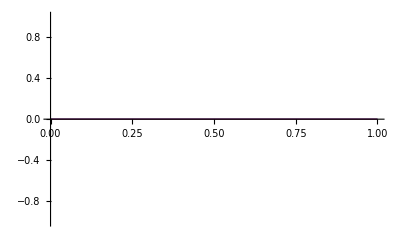

```mathematica
κ=1;
λ=1;
y=1;
Eig1[μ_]:=-((1+μ) ((-1+κ^2) λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2)
Eig2[μ_]:=((1+μ) (λ-κ^2 λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2)
Plot[{Eig1[μ],Eig2[μ]},{μ,0,1}]
```

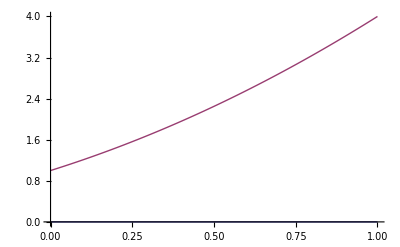

```mathematica
Clear[κ]
Clear[λ]
Clear[y]
κ=0;
λ=(1+μ)/2;
y=1;
Eig1[μ_]:=-((1+μ) ((-1+κ^2) λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2)
Eig2[μ_]:=((1+μ) (λ-κ^2 λ+√((-1+κ^2) ((-1+κ^2) λ^2+2 κ (-1+μ) μ^(2 y) (1+κ^2+2 κ μ)))))/((1+κ^2+2 κ μ)^2)
Plot[{Eig1[μ],Eig2[μ]},{μ,0,1}]
```

```mathematica
d
```

```mathematica
(* Recursive equation plots*)
f1[x_]:=(μ^(2 y) (1+μ) (1+x)^2)/(2 (1+2 μ*x+x));
```

```mathematica
(*HN3 A[1] fixed point solution; only 2 fixed point A[1]=0 or 1 because μ≥1, A[1]≥0*)
y=0;
Simplify[Solve[A[1]==(2 (1+μ) A[1])/(1+2 μ A[1]+A[1]^2)*(μ^(2 y) (1+μ) (1+A[1])^2)/(2 (1+2 μ A[1]+A[1]^2)), A[1] ],A[1]≥0&&μ≥1]
f[0]
Factor[f[1]]
Clear[y]
```

{{A[1]→0},{A[1]→1},{A[1]→-μ},{A[1]→1/2 (-1-3 μ-√(-7+2 μ+9 μ^2))},{A[1]→1/2 (-1-3 μ+√(-7+2 μ+9 μ^2))}}

(1+μ)/2

1

```mathematica
(*HN5 A[1] fixed point solution, A[1]≥1, μ≥1*)
Solve[A[1]==(2 (1+μ) A[1])/(1+2 μ A[1]+A[1]^2)*(μ^(2 y) (1+μ) (1+A[1])^2)/(2 (1+2 μ A[1]+A[1]^2)), A[1] ]
```

{{A[1]→0},{A[1]→1/2 (-2 μ+μ^y+μ^(1+y)-√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))},{A[1]→1/2 (-2 μ+μ^y+μ^(1+y)+√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))},{A[1]→1/2 (-2 μ-μ^y-μ^(1+y)-√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))},{A[1]→1/2 (-2 μ-μ^y-μ^(1+y)+√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))}}

```mathematica
y=-2.0;
Solve[1/2 (-2 /μ+μ^-y+μ^(-1-y)+√(4 (-1+μ^-y+μ^(-1-y))+(-2 /μ+μ^-y+μ^(-1-y))^2))==0, μ, Reals]
Clear[y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μ→0.618034}}

```mathematica
Factor[Simplify[Expand[(2 /μ-μ^-y-μ^(-1-y))^2 -4 (-1+μ^-y+μ^(-1-y))-(-2 /μ+μ^-y+μ^(-1-y))^2]]]
```

4 μ^(-1-y) (-1-μ+μ^(1+y))

```mathematica
(-2 μ+μ^y+μ^(1+y))^2-4 (-1+μ^y+μ^(1+y))-(-2 μ+μ^y+μ^(1+y))^2
```

-4 (-1+μ^y+μ^(1+y))

```mathematica
y=-1.25;
Solve[-1+μ^y+μ^(1+y)==0, μ,Reals]
Clear[y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μ→3.0796}}

```mathematica
Plot3D[1/2 (-2 /μ+μ^-y+μ^(-1-y)+√(4 (-1+μ^-y+μ^(-1-y))+(-2 /μ+μ^-y+μ^(-1-y))^2)),{μ,0,1},{y,-2,0},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (-2 /μ-μ^-y-μ^(-1-y)+√(-4 (1+μ^-y+μ^(-1-y))+(2 /μ+μ^-y+μ^(-1-y))^2)),{μ,0,1},{y,-2,0},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Solve[1/2 (-μ+μ^2+√(-4+4 μ+5 μ^2-2 μ^3+μ^4))==0,μ]
```

{{μ→1/2 (-1+√5)}}

```mathematica
(* Plots of 1/μ*)
```

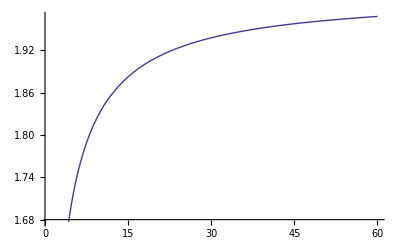

```mathematica
f2[m_]:=2*m^(2+2y)*(m+1)/(m^4+2m^3+1)
y=0.5;
Plot[f2[m],{m, 1, 60}]
N[f2[100000000000000000],100]
Clear[y];
```

```mathematica
y=1000000;
N[Solve[μ^(1+y)+μ^y==1,μ, Reals]]
Clear[y];
```

{{μ→0.999999}}

```mathematica
Reduce[μ^(1+y)+μ^y==1]
```

μ^y==1-μ^(1+y)

```mathematica
Rationalize[0.754877666246692760049508896]
```

0.7548776662466927600495089

```mathematica
N[Log[3/2]/Log[2]]
```

0.584963